Caso I

```mathematica
Manipulate[StreamPlot[{c-y-x^2,y-x^2},{x,-2,2},{y,-2,2}],{c,-1,1}]
```

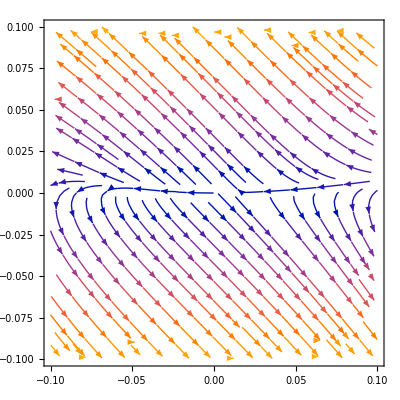

```mathematica
StreamPlot[{-y-x^2,y-x^2},{x,-0.1,0.1},{y,-0.1,0.1}]
```

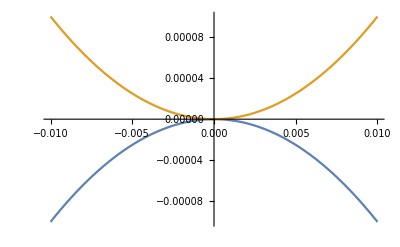

```mathematica
Plot[{-x^2,x^2},{x,-0.01,0.01}]
```

```mathematica
J1=({{D[c-y-x^2,x], D[c-y-x^2,y]}, {D[y-x^2,x], D[y-x^2,y]}})
```

{{-2 x,-1},{-2 x,1}}

```mathematica
MatrixForm[J]
```

(-2 x | -1
-2 x | 1)

```mathematica
Tr[J1]
```

1-2 x

```mathematica
Det[J1]
```

-4 x

```mathematica
disc1=Tr[J1]^2-4*Det[J1]
```

(1-2 x)^2+16 x

```mathematica
Solve[disc1==0,x]
```

{{x→1/2 (-3-2 √2)},{x→1/2 (-3+2 √2)}}

```mathematica
N[{{x->1/2 (-3-2 √2)},{x->1/2 (-3+2 √2)}}]
```

{{x→-2.91421},{x→-0.0857864}}

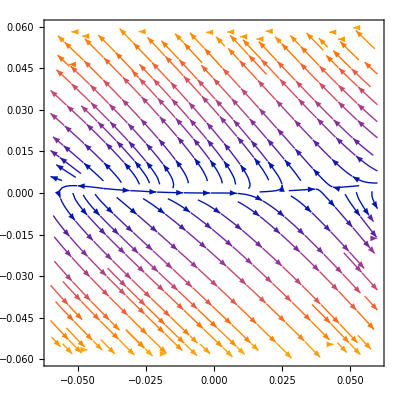

```mathematica
StreamPlot[{2*(0.04)^2-y-x^2,y-x^2},{x,-0.06,0.06},{y,-0.06,0.06}]
```

```mathematica
ev1=Eigenvectors[J1/.{x->-0.04}]
```

{{0.772219,-0.635356},{-0.995306,0.0967765}}

```mathematica
m1=ev1[[1]][[2]]/ev1[[1]][[1]]
```

-0.822767

```mathematica
m2=ev1[[2]][[2]]/ev1[[2]][[1]]
```

-0.0972329

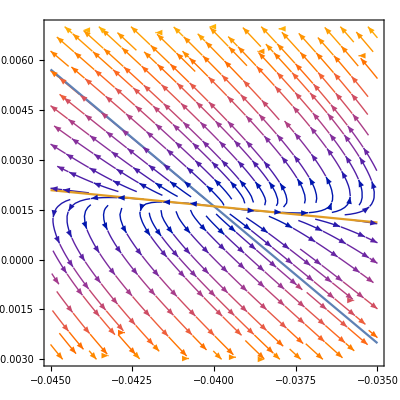

```mathematica
Show[StreamPlot[{2*(0.04)^2-y-x^2,y-x^2},{x,-0.045,-0.035},{y,-0.003,0.007}],Plot[{m1*x+(0.04^2+m1*0.04),m2*x+(0.04^2+m2*0.04)},{x,-0.045,-0.035}]]
```

```mathematica
Solve[D[disc1,x]==0,x]
```

{{x→-3/2}}

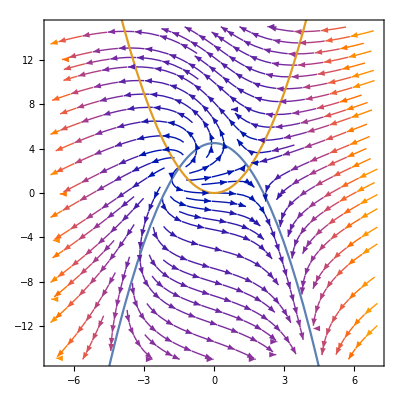

```mathematica
Show[StreamPlot[{2*(3/2)^2-y-x^2,y-x^2},{x,-7,7},{y,-15,15}],Plot[{2*(3/2)^2-x^2,x^2},{x,-7,7}]]
```

```mathematica
ev2=Eigenvectors[J1/.{x->3/2}]
```

{{1/3 (2+√7),1},{1/3 (2-√7),1}}

```mathematica
N[ev2]
```

{{1.54858,1.},{-0.21525,1.}}

```mathematica
sst1=NDSolve[{x'[t]==2*(3/2)^2-y[t]-x[t]^2,y'[t]==y[t]-x[t]^2,x[200]==3/2-(2+Sqrt[7])/3000,y[200]==9/4-1/1000},{x,y},{t,0,200}]
sust1=NDSolve[{x'[t]==2*(3/2)^2-y[t]-x[t]^2,y'[t]==y[t]-x[t]^2,x[0]==3/2+(2-Sqrt[7])/3000,y[0]==9/4+1/1000},{x,y},{t,0,200}]
```

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…]}}

NDSolve::ndsz: At t == 5.99879, step size is effectively zero; singularity or stiff system suspected.

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…]}}

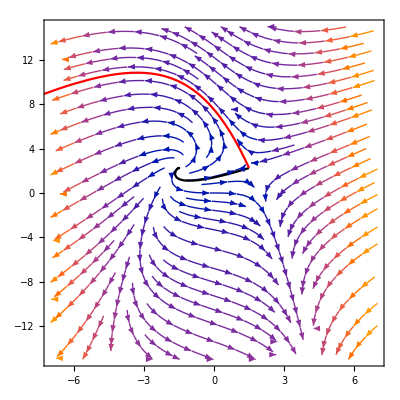

```mathematica
Show[StreamPlot[{2*(3/2)^2-y-x^2,y-x^2},{x,-7,7},{y,-15,15}],ParametricPlot[Evaluate[{x[t],y[t]}/.sst1],{t,0,200},PlotStyle->Black],ParametricPlot[Evaluate[{x[t],y[t]}/.sust1],{t,0,5.9},PlotStyle->Red]]
```

```mathematica
frames=ParallelTable[StreamPlot[{2*(x0^2)-y-x^2,y-x^2},{x,-x0-x0,x0+x0},{y,x0^2-2*x0,x0^2+2*x0}],{x0,0.01,4,0.01}];
```

```mathematica
mov1=ListAnimate[frames]
```

```mathematica
Export["bifurcacion.gif",frames,CompressionLevel->0]
```

bifurcacion.gif

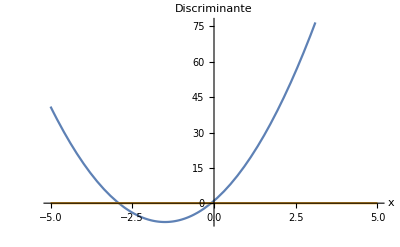

```mathematica
Plot[{disc1,0},{x,-5,5},AxesLabel->{x,"Discriminante"}]
```

En este caso vemos que obtenemos una transición silla-nodo pero donde ambos son inestables (NUEVO!), este nodo se convierte en una espiral, y finalmente esta espiral se vuelve a convertir en un nodo.

```mathematica
Eigensystem[J/.{x->0}]
```

{{1,0},{{-1,1},{1,0}}}

```mathematica
FindRoot[4*x^2+12*x+1==0,{x,1}]
```

{x→-0.0857864}

```mathematica
4*x^2+12*x+1/.{x->-10}
```

281

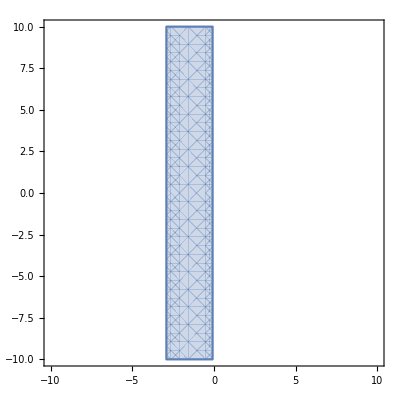

```mathematica
RegionPlot[4*x^2+12*x+1<0,{x,-10,10},{y,-10,10}]
```

```mathematica
Solve[4*x^2+12*x+1==0,{x}]
```

{{x→1/2 (-3-2 √2)},{x→1/2 (-3+2 √2)}}

```mathematica
N[{{x->1/2 (-3-2 √2)},{x->1/2 (-3+2 √2)}}]
```

{{x→-2.91421},{x→-0.0857864}}

Caso II

```mathematica
Manipulate[StreamPlot[{y-x^2,c-y-x^2},{x,-2,2},{y,-2,2}],{c,-1,1}]
```

```mathematica
J2=({{D[y-x^2,x], D[y-x^2,y]}, {D[c-y-x^2,x], D[c-y-x^2,y]}})
```

{{-2 x,1},{-2 x,-1}}

```mathematica
MatrixForm[J]
```

(-2 x | 1
-2 x | -1)

```mathematica
Tr[J2]
```

-1-2 x

```mathematica
Det[J2]
```

4 x

```mathematica
disc2=Tr[J2]^2-4*Det[J2]
```

(-1-2 x)^2-16 x

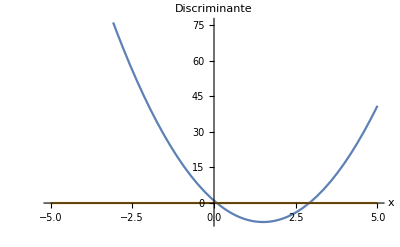

```mathematica
Plot[{disc2,0},{x,-5,5},AxesLabel->{x,"Discriminante"}]
```

En este caso vemos que obtenemos una transición silla-nodo común y corriente, pero al igual que en el caso anterior, este nodo se convierte en una espiral, y finalmente esta espiral se vuelve a convertir en un nodo.

Es interesante observar que ambos casos ocurren con ceroclinas idénticas, sólo que para un caso una ceroclina corresponde a la ecuación de la componente x y la otra para la componente y, y para el segundo caso corresponden de la forma inversa. Este cambio también sucede cuando multiplicamos cada sistema por -1.